# Лабораторная работа “Численное решение обыкновенных дифференциальных уравнений”

## Задание

Дана задача Коши для ОДУ. Решить эту задачу на данном интервале [x_0,X] аналитически или численно (самостоятельно или с помощью Mathematica или любой другой программы). Разрешается вместо задачи из варианта взять любую задачу небесной или земной механики.

Построить график полученного решения, вычислить значение решения в точке X. Если дана система ОДУ, необходимо построить графики каждой компоненты решения.

Написать программу, которая решает данную задачу Коши соответствующим вашему варианту численным методом с адаптивным выбором шага по правилу Рунге (см. конспект). Если метод многошаговый – используйте фиксированный шаг, стартовые значения следует брать из решения, полученного в пункте 1. Если ОДУ имеет порядок выше первого, его необходимо предварительно свести к системе первого порядка путем введения вспомогательных переменных.

Построить точечные графики численного решения, полученного количестве шагов около N=200, совместить их с графиками из пункта 2.

Построить логарифмическую диаграмму сходимости. Для многошаговых методов с постоянным шагом по оси абсцисс на диаграмме откладывается величина шага h, соответствующая количеству отрезков N=10^k, k=1,2,...,6. Для одношаговых методов с адаптивной сеткой по оси абсцисс откладывается требуемая величина локальной погрешности ε=10^-k, k=1,2,...,10. По оси ординат откладывается погрешность r_N=|y(X)-y_N|. Здесь y(X) – точное решение, вычисленное в пункте 2, y_N – приближенное решение, полученное вашей программой.

Составить отчет, который содержит

Описание решения задачи Коши из пункта 1. Если используются сторонние программы – привести команды, с помощью которых получено решение.

Сведение к системе первого порядка (если решается уравнение порядка выше 1)

Совмещенные графики точного и приближенного решений из пункта 4

Диаграмма из пункта 5

Код программы

### Методы

Явный метод средних прямоугольников

Метод Рунге–Кутты, задаваемый таблицей Бутчера
 0 | 0 | 0
1 | 1 | 0
 | 1/2 | 1/2

Явный метод Рунге–Кутты третьего порядка (любой)

Явный метод Рунге–Кутты четвертого порядка (любой)

Метод Рунге–Кутты, задаваемый таблицей Бутчера
 0 | 0 | 0
2/3 | 1/3 | 1/3
 | 1/4 | 3/4

Метод Рунге–Кутты, задаваемый таблицей Бутчера
 a | a | 0
1-a | 1-2a | a
 | 1/2 | 1/2, a=(3+√3)/6

Двухшаговый явный метод Адамса

Трехшаговый явный метод Адамса

Двухшаговый неявный метод Адамса

Трехшаговый неявный метод Адамса

Метод ФДН третьего порядка

### Задачи

y''= -x sin y   , y(x_0)=2, y'(x_0)=1 , [x_0,X]=[-10,10]

y''(x)==2 y(x) cos(π x),y(0)==1,y'(0)==2 , [x_0,X]=[0,10]

y''(x)==y(x) sin(π x)-2 y'(x),y(0)==1,y'(0)==0, [x_0,X]=[0,10]

y''(x)==-2 y(x) cos(x) y'(x),y(0)==1,y'(0)==-1,[x_0,X]=[0,10]}

y''(x)==-2 y'(x) (y'(x)+2 y(x) cos(3 π x)),y(0)==3,y'(0)==1,[x_0,X]=[0,10]

y''(x)==y(x) cos(x/2)-2 y'(x),y(0)==3,y'(0)==1,[x_0,X]=[0,33]

y''(x)==-2 y'(x)-5 y(x)+cos(x),y(0)==3,y'(0)==1,[x_0,X]=[0,10]

y'''(x)==-2 y''(x)-y(x),y(0)==3,y'(0)==1,y''(0)==2,[x_0,X]=[0,30]

u'(x)==3 u(x)-2 u(x) v(x),v'(x)==u(x) v(x)-2 v(x),u(0)==2,v(0)==1,[x_0,X]=[0,10]

u''(x)==-(2 u(x))/(((u(x))^2+(v(x))^2)^(3/2)),v''(x)==-(v(x))/(((u(x))^2+(v(x))^2)^(3/2)),u(0)==2,v(0)==1,u'(0)==0.01,v'(0)==0.03,[x_0,X]=[0,10]

x'(t)==-3 (x(t)-y(t)),y'(t)==x(t) (-z(t))+26.5 x(t)-y(t),z'(t)==x(t) y(t)-z(t),x(0)==z(0)==0,y(0)==1,[x_0,X]=[0,10]

### Решение задачи Коши в Mathematica

#### Точное (символьное решение)

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{v→Function[{x},1-Tanh[x/(√2)]^2],u→Function[{x},2-√2 Tanh[x/(√2)]]}

{0.585788,2.88541×10^-6}

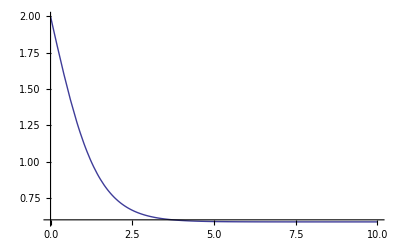

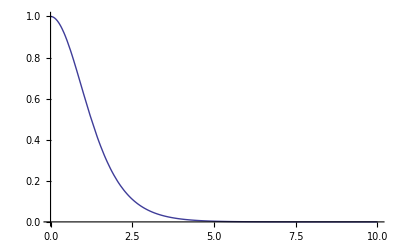

```mathematica
sol=DSolve[
{(*список уравнений и начальных условий*)
(*внимание! знак равенства должен быть двойным: "==", а не "=" *)
u'[x]==-v[x],(*уравнение 1*)
v'[x]==-2v[x]+u[x]v[x],(*уравнение 2*)
u[0]==2,(*начальное условие 1*)
v[0]==1 (*начальное условие 2*)
},
{u,v},(*список неизвестных*)
x (*аргумент*)
]⟦1⟧
{u[10],v[10]}/.sol//N(*вычисляем решение в точке х=10*)

(*рисуем графики*)
Plot[u[x]/.sol,{x,a,b},PlotRange->All,PlotStyle->Thick]
Plot[v[x]/.sol,{x,a,b},PlotRange->All,PlotStyle->Thick]
```

#### Численное (приближенное) решение

```mathematica
sol=NDSolve[
{(*список уравнений и начальных условий (точно так же как в символьном решении) *)
u'[x]==-v[x],
v'[x]==-2v[x]+u[x]v[x],
u[0]==2,
v[0]==1},
{u,v},(*неизвестные*)
{x,0,10},(*аргумент и границы его изменения, {x,x0,X}*)
AccuracyGoal->13 (*требование к точности*)
]⟦1⟧
{u[10],v[10]}/.sol(*вычисляем решение в точке 10*)

(*графики*)

{a,b}={0,10}
Plot[u[x]/.sol,{x,a,b},PlotRange->All,PlotStyle->Thick]
Plot[v[x]/.sol,{x,a,b},PlotRange->All,PlotStyle->Thick]
```

{u→InterpolatingFunction[…],v→InterpolatingFunction[…]}

{0.585788,2.88541×10^-6}

{0,10}

-Graphics-

-Graphics-

```mathematica
{0.5857884941872299,2.8854077717843646*^-6}
```